```mathematica
(*SetDirectory["E:\\work\\thesis\\论文\\nb\\"];*)
```

```mathematica
Clear["@"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear will be suppressed during this calculation.

```mathematica
<<Data`;
<<Bisfit`;
<<Matcher`;
```

```mathematica
(*dd=Reap[
For[i=51,i≤81,i++,
Sow[Import["ca_"<>ToString[i]<>".txt","Table"]];
]];
Dimensions[dd[[2,1]]]
dd[[2,1]];*)
Needs["PlotLegends`"];
```

```mathematica
data=ColeData[];
Dimensions[data]
```

{32,8,4}

## how is cole fit data

```mathematica
Max[data[[;;,;;,1]]]
Max[data[[;;,;;,2]]]
Max[data[[;;,;;,3]]]
Max[data[[;;,;;,4]]]
Min[data[[;;,;;,1]]]
Min[data[[;;,;;,2]]]
Min[data[[;;,;;,3]]]
Min[data[[;;,;;,4]]]
```

Max[1.57236×10^6,51.52257803911647+56.311895874767295*I,98.13004269718655+80.01678387340989*I,98.67911505275761+25.09819021181368*I]

Max[110.991,51.52257803911647-56.311895874767295*I,98.13004269718655-80.01678387340989*I,98.67911505275761-25.09819021181368*I]

Max[1.85557,2.-0.2052493825986385*I,2.-0.3745258442098394*I,2.-0.47714002680445233*I]

3.27306×10^28

Min[66.6085,51.52257803911647+56.311895874767295*I,98.13004269718655+80.01678387340989*I,98.67911505275761+25.09819021181368*I]

Min[-915543.,51.52257803911647-56.311895874767295*I,98.13004269718655-80.01678387340989*I,98.67911505275761-25.09819021181368*I]

Min[0.173781,2.-0.2052493825986385*I,2.-0.3745258442098394*I,2.-0.47714002680445233*I]

-503447.

```mathematica
(*filter fitted data*)
(* there are some imaginary numbers, must remove them*)
fdata=Map[Filterd[#]&,data];
Dimensions[%]
Total[Map[Dimensions[#]&,fdata][[All,1]]]/(32*8)
```

```mathematica
Max[fdata[[;;,;;,1]]]
Max[fdata[[;;,;;,2]]]
Max[fdata[[;;,;;,3]]]
Max[fdata[[;;,;;,4]]]
Min[fdata[[;;,;;,1]]]
Min[fdata[[;;,;;,2]]]
Min[fdata[[;;,;;,3]]]
Min[fdata[[;;,;;,4]]]
Table[Mean[Flatten[fdata[[;;,;;,i]]]],{i,4}]
(* this looks more reasonable*)
```

161.606

74.349

0.897999

99490.

77.4994

27.7637

0.361436

2942.16

{102.698,48.497,0.682972,32407.9}

The 4th measure is interesting, why is it like this...

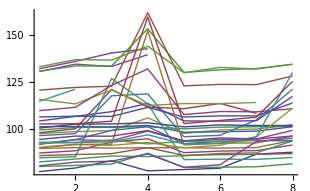
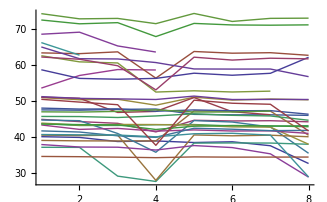
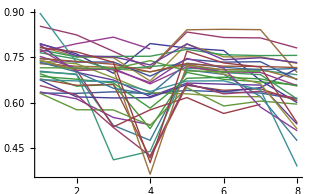
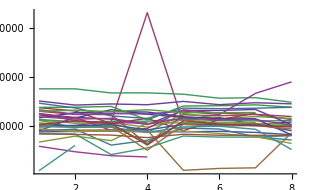

```mathematica
Table[ListPlot[fdata[[All,All,i]],Joined->True],{i,4}]
```

```mathematica
fdata//MatrixForm;
```

## 类概率密度

```mathematica
d1=Table[StandardDeviation[Flatten[fdata[[All,All,i]]]],{i,3}]
Mdistance[u_,v_]:=√(∑ _(i=1)^Length[u] ((u[[i]]-v[[i]])/d1[[i]])^2);
```

```mathematica
ddiff=Flatten[Reap[For[i=1,i≤15,i++,
For[j=i+1,j≤i+3,j++,
Sow[Flatten[Outer[EuclideanDistance,fdata[[i]],fdata[[j]],1]]]
]]
][[2,1]]];
dsame=Reap[For[i=1,i≤15,i++,
For[j=1,j≤Length[fdata[[i]]]-1,j++,
For[k=j+1,k<=Length[fdata[[i]]],k++,
Sow[EuclideanDistance[fdata[[i]][[j]],fdata[[i]][[k]]]];
(*Sow[-Mdistance[fdata[[i]][[j]],fdata[[i]][[k]]]];*)
]]]
][[2,1]];
Pd=Length[ddiff]/(Length[dsame]+Length[ddiff]);
Ps=Length[dsame]/(Length[dsame]+Length[ddiff]);
```

```mathematica
mdsame=Mean[dsame]
mddiff=Mean[ddiff]
ddsame=StandardDeviation[dsame]
dddiff=StandardDeviation[ddiff]
Ns=Length[dsame]
Nd=Length[ddiff]
Max[ddiff]
Max[dsame]
```

5.43135

20.2124

5.87318

13.4915

307

1922

55.0484

26.8119

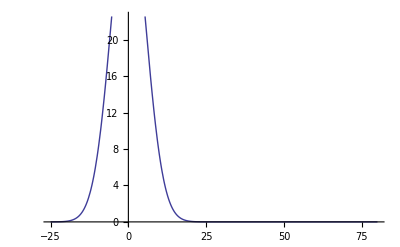

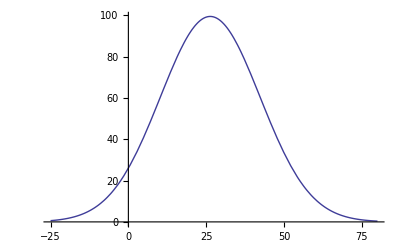

```mathematica
(*Ppdf1=Plot[500*PDF[NormalDistribution[mdsame,ddsame-7],x],{x,-25,80}]
Ppdf2=Plot[4000*PDF[NormalDistribution[mddiff,dddiff],x],{x,-25,80}]*)
```

```mathematica
sdsame=MovingAverage[dsame,{1,1,1}];
sddiff=MovingAverage[ddiff,{1,1,1}];
```

```mathematica
h1=Histogram[sdsame,{0,10,0.3},"ProbabilityDensity",(*"Probability",*)ColorFunction->Function[{x},Black]]
(*h1=Histogram[Ps*sdsame,{0,10,0.1},"Probability",ColorFunction->Function[{x},Black]]*)
(*BinCounts[Flatten[ds[[2,1]],1],1]*)
```

-Graphics-

```mathematica
(*Show[Ppdf1,h1,PlotRange->{{-5,25},{0,80}}]*)
```

-Graphics-

```mathematica
h2=Histogram[sddiff,{0,30,0.3},"ProbabilityDensity"]
```

-Graphics-

```mathematica
(*Show[Ppdf2,h2,PlotRange->{{0,100},{0,100}}]*)
Histogram[{sddiff,sdsame},{0,32,0.3},"ProbabilityDensity",PlotRange->{{0,30},{0,0.25}}]
```

-Graphics-

```mathematica
Show[h2,h1,PlotRange->{{0,30},{0,0.5}}]
```

-Graphics-

```mathematica
(*first *)
(*Pd=Length[ddiff]/(Length[dsame]+Length[ddiff]);
Ps=Length[dsame]/(Length[dsame]+Length[ddiff]);*)
(*find when his1=his2 条件概率密度*)
bcdiff=Pd*BinCounts[ddiff,{0,15,0.1}]*10/Nd;
bcsame=Ps*BinCounts[dsame,{0,20,0.1}]*10/Ns;
Ps
Pd
ListPlot[{bcdiff,bcsame}];
l=Min[Length[bcdiff],Length[bcsame]];
dbc=bcsame[[1;;l]]-bcdiff[[1;;l]];
sdbc=MovingAverage[dbc,{1,1,1}];
t=1;k=1;
For[i=1,i≤l,i++,
If[sdbc[[i]]>0,t=i,
If[sdbc[[i]]<0,k=i;Break[],]
]
]
thd=(t+k)/2*0.1
```

307/2229

1922/2229

2.45

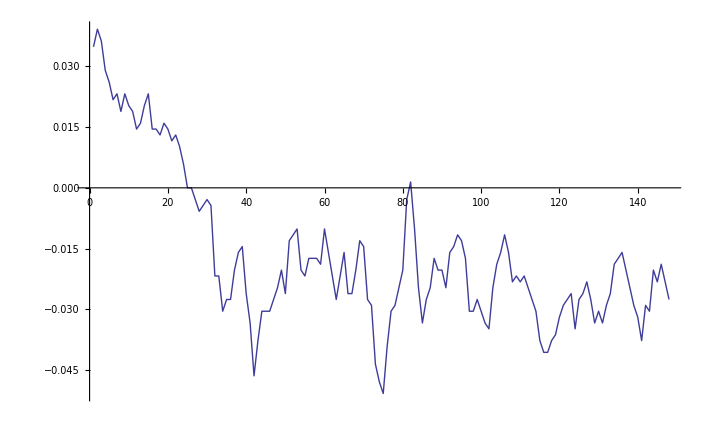

```mathematica
ListLinePlot[sdbc]
```

```mathematica
(*For[i=1,i≤Length[ddiff],i,
If[ddiff[i]>200000,ddiff=Delete[ddiff,i],i++]];*)
```

```mathematica
(*Position[ddiff,Select[ddiff,#>200000&]]
Length[tdd]*)
```

```mathematica
ddiff2=Flatten[Reap[For[i=15,i≤30,i++,
For[j=i+1,j≤31,j++,
Sow[Flatten[Outer[EuclideanDistance,fdata[[i]],fdata[[j]],1]]]
]]
][[2,1]]];
dsame2=Reap[For[i=15,i≤31,i++,
For[j=1,j≤Length[fdata[[i]]]-1,j++,
For[k=j+1,k<=Length[fdata[[i]]],k++,
Sow[EuclideanDistance[fdata[[i]][[j]],fdata[[i]][[k]]]];
(*Sow[-EuclideanDistance[fdata[[i]][[j]],fdata[[i]][[k]]]];*)
]
]
]
][[2,1]];
(*using threshold*)
(*N[Length[Select[ddiff2,#≥thd&]]/Length[ddiff2]]
N[Length[Select[dsame2,#≤(thd)&]]/Length[dsame2]]*)
```

```mathematica
(*using EER*)
err1=Plot[Length[Select[ddiff,#<(x)&]]/Length[ddiff],{x,0,100}];
err2=Plot[Length[Select[dsame,#>x&]]/Length[dsame],{x,0,100}];
```

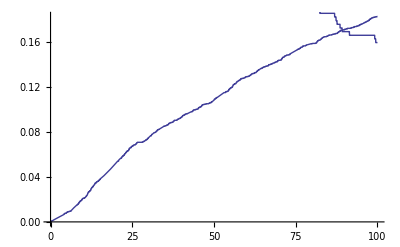

```mathematica
Show[err1,err2]
```

```mathematica
For[k=0.1,k<500,k=k+1,
If[Abs[Length[Select[ddiff,#≥(k)&]]/Length[ddiff]-
Length[Select[dsame,#≤(k)&]]/Length[dsame]]<0.05,Print[k];Break[];]
]
N[Length[Select[dsame,#≤(k)&]]/Length[dsame]]
N[Length[Select[ddiff2,#≥(k)&]]/Length[ddiff2]]
N[Length[Select[dsame2,#≤(k)&]]/Length[dsame2]]
```

9.1

0.814332

0.733726

0.882641

```mathematica
thd+k
```

20.35

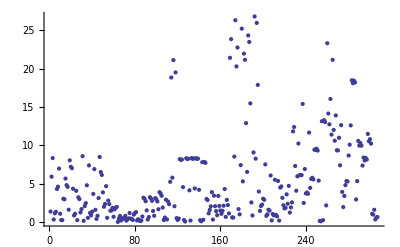

```mathematica
ListPlot[dsame]
```

```mathematica
(*try Parzen*)
(*gaussian window*)
parzen[N_,h1_,x_]:=Module[
{n,hn},
hn=h1/(√N);
Table[1/(N*hn)∑_(i=1)^N (1/(√(2 π)))ⅇ^(-1/2((x[[j]]-x[[i]])/hn)^2),{j,1,N}]

]
(*Nn=Ns;
hns=h1/(√Nn);
d=dsame;*)
fparzen[x_,d_,N_,h1_]:=1/(N*h1/(√N))∑_(i=1)^N (1/(√(2 π)))ⅇ^(-1/2((x-d[[i]])/(h1/(√N)))^2);
(*conditional probability*)

fps[x_]:=fparzen[x,dsame,Ns,2*√Ns];
fpd[x_]:=fparzen[x,ddiff,Nd,4*√Nd];
```

0.102268

```mathematica
pwsame=parzen[Ns,2*√Ns,dsame];
```

```mathematica
pwdiff=parzen[Nd,4*√Nd,ddiff];
```

```mathematica
Transpose[{dsame,pwsame}]//MatrixForm;
```

```mathematica
ppws=Labeled[ListPlot[Transpose[{dsame,pwsame}](*,Joined->True*),PlotStyle->{PointSize[0.006]},AxesLabel->{"d","p(d)"}],"h1=0.5*√Ns"];

ppwd=Labeled[ListPlot[Transpose[{ddiff,pwdiff}],PlotStyle->{PointSize[0.005]},AxesLabel->{"d","p(d)"}],"h1=1*√Nd"];
Length[pwsame];
```

```mathematica
Plot[{Ps*fps[x],Pd*fpd[x]},{x,0,50},PlotLegend->{"psame", "pdiff"}]
```

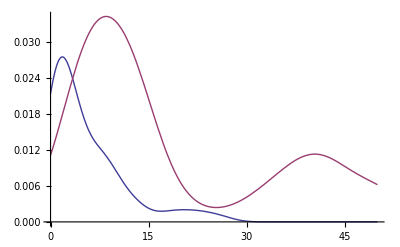

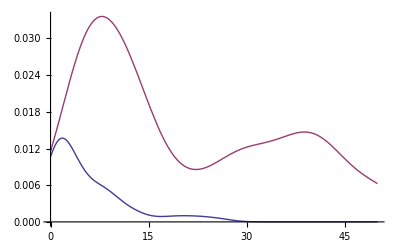

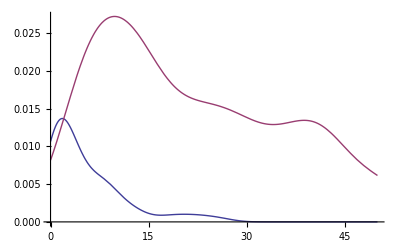

```mathematica
t=k=0;
For[x=0,x≤10,x+=0.01,
If[Abs[Ps*fps[x]-Pd*fpd[x]]<0.001,t=x;Break[],]
]
t
```

2.18

```mathematica
(*bayes classifier minimal err*)
Pe=∫_t^40 Ps*fps[y]ⅆy +∫_0^t Pd*fpd[z]ⅆz
```

0.111095

```mathematica
N[Length[Select[ddiff2,#≥(t)&]]/Length[ddiff2]]
N[Length[Select[dsame2,#≤(t)&]]/Length[dsame2]]

t1=N[Length[Select[ddiff,#≥(t)&]]/Length[ddiff]]
t2=N[Length[Select[dsame,#≤(t)&]]/Length[dsame]]
```

```mathematica
(1-t1)*Pd+(1-t2)*Ps
```

0.0861373

```mathematica
(*KNN 后验概率*)

Vn[x_,data_,kn_]:=Module[
{tt,dd},
tt=Map[Abs[x-#]&,data];
dd=Ordering[tt,kn];
tt=data[[dd]];
Max[tt]-Min[tt]
]

pknn[x_,Nn_,d_,kn_]:=kn/(Nn*Vn[x,d,kn]);
(*变量x的概率密度*) 
Pk[x_]:=pknn[x,Ns+Nd,Join[dsame,ddiff],Floor[4*√(Ns+Nd)]]
(*total vn*)
ki[x_,data_,kn_]:=Module[
{tt,dd,n1,n2},
tt=Map[Abs[x-#]&,Flatten[data]];
dd=Ordering[tt,kn];
(*tt=data[[dd]];*)
n1=Table[Length[data[[i]]],{i,Length[data]}];
For[j=1,j≤Length[dd],j++,
For[i=1;n2=n1[[i]],i≤Length[n1],i++;n2=n2+n1[[i]],
If[dd[[j]]-n2≤0,dd[[j]]=i;Break[];,]
]
];
BinCounts[dd,{1,Length[data]+1}]
]
(*Length[{dsame,ddiff}]*)
```

```mathematica
(*后验概率*)
(*pks[x_]:=pknn[x,Ns,dsame,Floor[4*√Ns]]*)
fki[x_]:=ki[x,{dsame,ddiff},Floor[1*√(Ns+Nd)]];
pin[x_]:=fki[x]/Floor[2*√(Ns+Nd)];
```

```mathematica
pin[20]
```

{3/47,44/47}

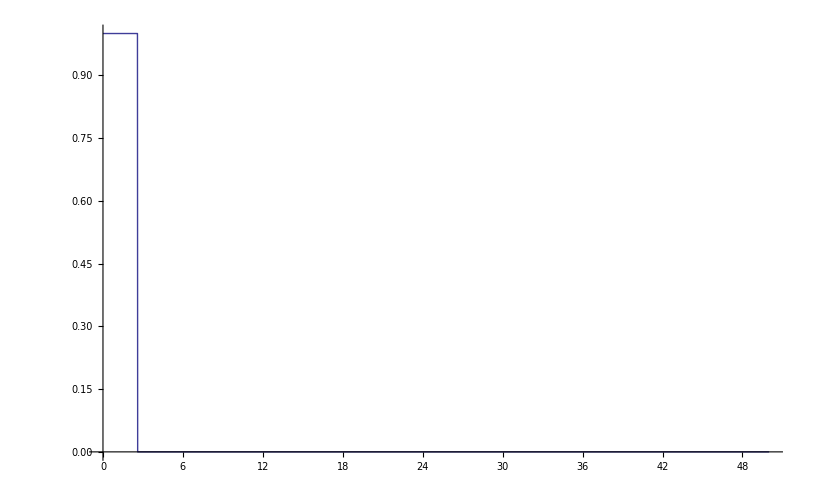

```mathematica
Plot[If[pin[x][[1]]>pin[x][[2]],1,0],{x,0,50},PlotRange->{{0,50},{0,1}}]
```

0.958478

0.594132

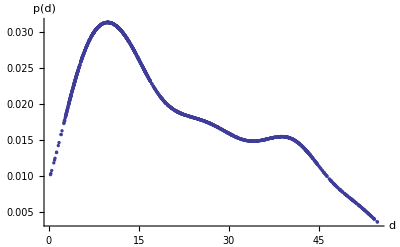
-Graphics-h1=4*√Nd

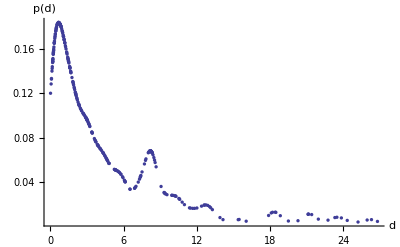
-Graphics-h1=0.5*√Ns

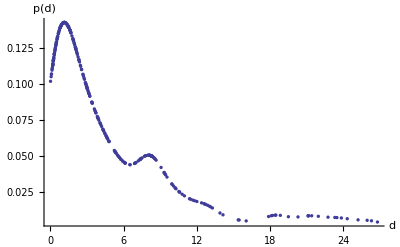
-Graphics-h1=1*√Ns

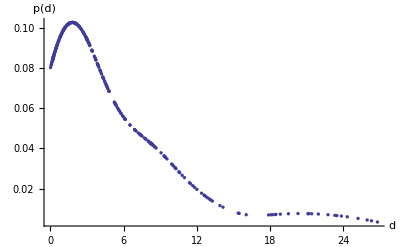
-Graphics-h1=2*√Ns

```mathematica
N[Length[Select[ddiff2,#≥(2.8)&]]/Length[ddiff2]]
N[Length[Select[dsame2,#≤(2.8)&]]/Length[dsame2]]
```

```mathematica
(**)
```

Export::infer: Cannot infer format of file pp.

$Failed